```mathematica
dictionary=Import["C:\\Program Files\\Wolfram Research\\Mathematica\\10.1\\SystemFiles\\Dictionaries\\English\\dictionary.txt"];
list=StringSplit[dictionary,"\n"];
```

```mathematica
arrows2[this_]:=StringTake[this,{1,-2}]->this

arrows[list_]:=DeleteDuplicates[Flatten[Table[Take[NestList[arrows2[#[[1]]]&,{list[[i]]},StringLength[list[[i]]]-1],{2,-1}],{i,1,Length[list]}],1]]

getCharList[lst_]:=With[{list=Select[lst,StringLength[#]>1&]},DeleteDuplicates[Table[StringTake[list[[i]],1],{i,Length[list]}]]]

getWordList[text_,replace_]:=Select[StringTrim[#]&/@StringSplit[StringReplace[ToLowerCase[text],replace]," "],#≠""&];

createLetterGraphs[text_,replace_]:=Module[{sL=Sort[DeleteDuplicates[getWordList[text,replace]]],char={}},char=getCharList[sL];Return[ListAnimate[Table[TreePlot[arrows[Select[sL,StringTake[#,1]==char[[i]]&]],Center,PlotLabel->char[[i]],VertexLabeling->Tooltip],{i,Length[char]}],AutoAction->False]]]
```

```mathematica
default={"-"->" ",","-> " ","!"-> " ","("->" ",")"->" ","?"-> " ","."-> " ","\""-> " ",";"-> " ","_"->" ","*"-> " ","'"->" ",":"->" "};
```

```mathematica
createLetterGraphs[ExampleData[{"Text","AliceInWonderland"}],default]
```

```mathematica
arrows[list_]:=DeleteDuplicates[Flatten[Table[Take[NestList[With[{t=#[[1]]},StringTake[t,{1,-2}]-> t]&,{list[[i]]},StringLength[list[[i]]]-1],{2,-1}],{i,1,Length[list]}],1]]

getCharList[lst_]:=With[{list=Select[lst,StringLength[#]>1&]},DeleteDuplicates[Table[StringTake[list[[i]],1],{i,Length[list]}]]]

getWordList[text_,replace_]:=Select[StringTrim[#]&/@StringSplit[StringReplace[ToLowerCase[text],replace]," "],#≠""&];

createLetterGraphs[text_,replace_]:=Module[{sL=Sort[DeleteDuplicates[getWordList[text,replace]]],char={}},char=getCharList[sL];Return[Table[TreePlot[arrows[Select[sL,StringTake[#,1]==char[[i]]&]],Center,PlotLabel->char[[i]],VertexLabeling->Tooltip],{i,Length[char]}]]]
```

```mathematica
DynamicModule[{text,p={"Text","AliceInWonderland"}},Column[{ActionMenu["Set x",{"AeneidEnglish":>(p={"Text","AeneidEnglish"};),"AliceInWonderland":>(p={"Text","AliceInWonderland"};),"BeowulfModern":>(p={"Text","BeowulfModern"};),"BeowulfOldEnglish":>(p={"Text","BeowulfOldEnglish"};),"CodeOfHammurabiEnglish":>(p={"Text","CodeOfHammurabiEnglish"};),"DeclarationOfIndependence":>(p={"Text","DeclarationOfIndependence"};),"DonQuixoteIEnglish":>(p={"Text","DonQuixoteIEnglish"};),"FederalistTen":>(p={"Text","FederalistTen"};),"FriendsRomansCountrymen":>(p={"Text","FriendsRomansCountrymen"};),"GenesisKJV":>(p={"Text","GenesisKJV"};),"GettysburgAddress":>(p={"Text","GettysburgAddress"};),"Hamlet":>(p={"Text","Hamlet"};),"JFKInaugural":>(p={"Text","JFKInaugural"};),"LesFleursDuMal":>(p={"Text","LesFleursDuMal"};),"OnTheNatureOfThingsEnglish":>(p={"Text","OnTheNatureOfThingsEnglish"};),"OriginOfSpecies":>(p={"Text","OriginOfSpecies"};),"PlatoMenoEnglish":>(p={"Text","PlatoMenoEnglish"};),"PrideAndPrejudice":>(p={"Text","PrideAndPrejudice"};),"Prufrock":>(p={"Text","Prufrock"};),"ShakespearesSonnets":>(p={"Text","ShakespearesSonnets"};),"TheRaven":>(p={"Text","TheRaven"};),"ToBeOrNotToBe":>(p={"Text","ToBeOrNotToBe"};)}],ListAnimate[createLetterGraphs[ExampleData[p]],AnimationRunning->False]}],Initialization:> {arrows[list_]:=DeleteDuplicates[Flatten[Table[Take[NestList[With[{t=#[[1]]},StringTake[t,{1,-2}]-> t]&,{list[[i]]},StringLength[list[[i]]]-1],{2,-1}],{i,1,Length[list]}],1]],getCharList[lst_]:=With[{list=Select[lst,StringLength[#]>1&]},DeleteDuplicates[Table[StringTake[list[[i]],1],{i,Length[list]}]]],getWordList[text_]:=Select[StringTrim[#]&/@StringSplit[StringReplace[ToLowerCase[text],{"-"->" ",","-> " ","!"-> " ","("->" ",")"->" ","?"-> " ","."-> " ","\""-> " ",";"-> " ","_"->" ","*"-> " ","'"->" ",":"->" "}]," "],#≠""&],createLetterGraphs[text_]:=Module[{sL=Sort[DeleteDuplicates[getWordList[text]]],char={}},char=getCharList[sL];Return[Table[TreePlot[arrows[Select[sL,StringTake[#,1]==char[[i]]&]],Center,PlotLabel->char[[i]],VertexLabeling->Tooltip],{i,Length[char]}]]]}]
```

```mathematica
Manipulate[u,{u,createLetterGraphs[ExampleData[{"Text","AliceInWonderland"}]]}]
```

```mathematica
Export[NotebookDirectory[]<>"KappaSquaredVisualization.cdf",nb,"CDF"]
```

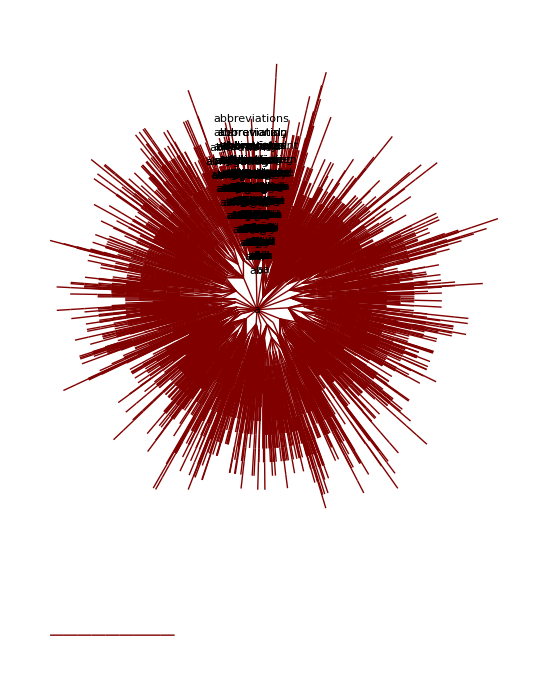

```mathematica
arrows2[this_]:=StringTake[this,{1,-2}]->this

arrows[list_]:=DeleteDuplicates[Flatten[Table[Take[NestList[arrows2[#[[1]]]&,{list[[i]]},StringLength[list[[i]]]-1],{2,-1}],{i,1,Length[list]}],1]]

getCharList[lst_]:=With[{list=Select[lst,StringLength[#]>1&]},DeleteDuplicates[Table[StringTake[list[[i]],1],{i,Length[list]}]]]

getWordList[text_]:=Select[StringTrim[#]&/@StringSplit[StringReplace[ToLowerCase[text],{"-"->" ",","-> " ","!"-> " ","("->" ",")"->" ","?"-> " ","."-> " ","\""-> " ",";"-> " ","_"->" ","*"-> " ","'"->" ",":"->" "}]," "],#≠""&];

generateEdges[text_]:=Module[{sL=Sort[DeleteDuplicates[getWordList[text]]],char={}},char=getCharList[sL];Return[Table[arrows[Select[sL,StringTake[#,1]==char[[i]]&]],{i,Length[char]}]]]

pickWord[text_,list_]:=Select[Select[Flatten[list],StringLength[#[[1]]]≥ StringLength[text]&],StringTake[#[[1]],{1,StringLength[text]}]==text&]
```

```mathematica
lst=generateEdges[ExampleData[{"Text","AliceInWonderland"}]]
```

{{abou→about,abo→abou,ab→abo,a→ab,abov→above,abo→abov,accusatio→accusation,accusati→accusatio,accusat→accusati,accusa→accusat,accus→accusa,accu→accus,acc→accu,ac→acc,a→ac,accustome→accustomed,accustom→accustome,258,atten→attend,atte→atten,authorit→authority,authori→authorit,author→authori,autho→author,auth→autho,aut→auth,au→aut,a→au,awa→away,aw→awa,a→aw,awhil→awhile,awhi→awhil,awh→awhi,aw→awh},23,{1}}
 |  |  |  |

```mathematica
Manipulate[TreePlot[pickWord[ToString[txt],lst],Left,ToString[txt],VertexLabeling->True],{txt,"a","String"},ControlType->InputField]
```

```mathematica
Clear[Evaluate[Context[]<>"*"]]
```

```mathematica
nb=CreateDocument[Manipulate[With[{t=pickWord[ToString[txt],generateEdges[ExampleData[{"Text",source}]]]},If[t≠{},TreePlot[t,Automatic,ToString[txt],VertexLabeling->True],"No graph for these letters"]],{{txt,"yo","String"},ControlType->InputField},{source,{"AliceInWonderland","DeclarationOfIndependence","Hamlet","OriginOfSpecies"}},Initialization:>{arrows[list_]:=DeleteDuplicates[Flatten[Table[Take[NestList[With[{t=#[[1]]},StringTake[t,{1,-2}]-> t]&,{list[[i]]},StringLength[list[[i]]]-1],{2,-1}],{i,1,Length[list]}],1]],getCharList[lst_]:=With[{list=Select[lst,StringLength[#]>1&]},DeleteDuplicates[Table[StringTake[list[[i]],1],{i,Length[list]}]]],getWordList[text_]:=Select[StringTrim[#]&/@StringSplit[StringReplace[ToLowerCase[text],{"-"->" ",","-> " ","!"-> " ","("->" ",")"->" ","?"-> " ","."-> " ","\""-> " ",";"-> " ","_"->" ","*"-> " ","'"->" ",":"->" "}]," "],#≠""&],generateEdges[text_]:=Module[{sL=Sort[DeleteDuplicates[getWordList[text]]],char={}},char=getCharList[sL];Return[Table[arrows[Select[sL,StringTake[#,1]==char[[i]]&]],{i,Length[char]}]]],pickWord[text_,list_]:=Select[Select[Flatten[list],StringLength[#[[1]]]≥ StringLength[text]&],StringTake[#[[1]],{1,StringLength[text]}]==text&]}]]
```

sg2v5_shm40FrontEndObject[LinkObject["sg2v5_shm", 3, 1]]40Untitled-1

```mathematica
Sort[pickWord["pi",lst],StringLength[#1[[1]]]<StringLength[#2[[1]]]&]
```

{pi→pic,pi→pie,pi→pig,pi→pin,pic→pick,pic→pict,pie→piec,pig→pige,pin→pine,pin→pink,pick→picke,pick→picki,pict→pictu,piec→piece,pige→pigeo,pine→pinea,picke→picked,picki→pickin,pictu→pictur,piece→pieces,pigeo→pigeon,pinea→pineap,pickin→picking,pictur→picture,pineap→pineapp,picture→pictures,pineapp→pineappl,pineappl→pineapple}

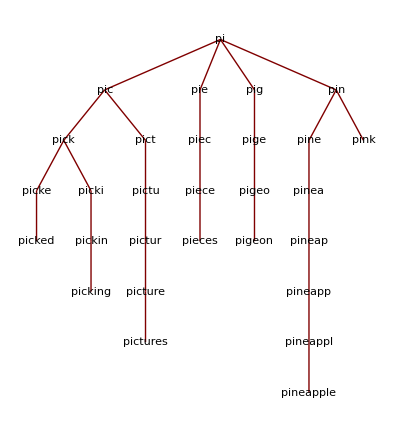

```mathematica
TreePlot[pickWord["pi",lst],Top,VertexLabeling->True,PlotRangePadding->Scaled[0.1]]
```